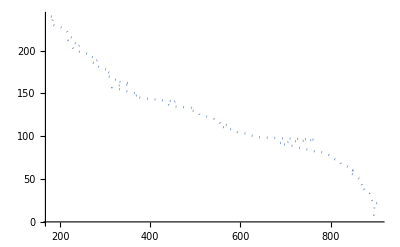

```mathematica
p=ListLinePlot[Import["/home/aaron/Developer/robotics/micromouse/plots/rightdiag.full","Table"],PlotStyle->Dotted]
```

```mathematica
Manipulate[Show[p,Plot[a*(x-b)^c+d,{x,50,950}]],{a,0.1,3000},{b,-800,100},{c,-1,-0.001},{d,-400,0}]
```